```mathematica
SetDirectory["/Users/BACCH-SP-1b/Programming/Projects/LogCompensatedOctaveSmooth"];
```

```mathematica
logOctaveSmoothLink = Install["/Users/BACCH-SP-1b/Programming/Projects/LogCompensatedOctaveSmooth/logCompensatedOctaveSmooth"]
```

LinkObject[…]

```mathematica
LinkPatterns[logOctaveSmoothLink]
```

{LogCompensatedOctaveSmooth[fractionDenominator_Real,windowType_Integer,data_List]}

```mathematica
?LogCompensatedOctaveSmooth
```

LogCompensatedOctaveSmooth[N, winType, data] applies a 1/Nth octave smoothing filter to data using a window (0 for rectangular, otherwise Hanning).

```mathematica
LongIR = Import["IRref.aiff"][[1,1,1]];
MaxPos = Position[Abs[LongIR],Max[Abs[LongIR]]][[1,1]];
RawTF = Fourier[LongIR[[MaxPos-100;;MaxPos-100+2047]],FourierParameters->{1,-1}];
FreqVec = Range[0,2047] 96000/2048;
```

#### Wrapping Function

```mathematica
logOctaveSmooth[data_,frac_,oSwindowType_]:=LogCompensatedOctaveSmooth[N[frac],Round[oSwindowType],data];
```

#### Speed comparison

```mathematica
realOctaveSmoothlink = Install["/Library/Application Support/BACCH-dSP/realOctaveSmooth"];
octaveSmooth[data_,frac_,oSwindowType_]:=RealOctaveSmooth[N[frac],Round[oSwindowType],data];
```

```mathematica
AbsoluteTiming[LogSmoothTFdB = logOctaveSmooth[20Log10[Abs[RawTF]],6,1];]
AbsoluteTiming[OldSmoothTFdB = octaveSmooth[20Log10[Abs[RawTF]],12,1];]
AbsoluteTiming[RefSmoothTFdB = 20Log10[Abs[LogCompensatedWeightsSmooth[RawTF,6,"Hanning","dB"]]];]
```

{0.015189,Null}

{0.011414,Null}

{0.287002,Null}

#### Smoothing comparison

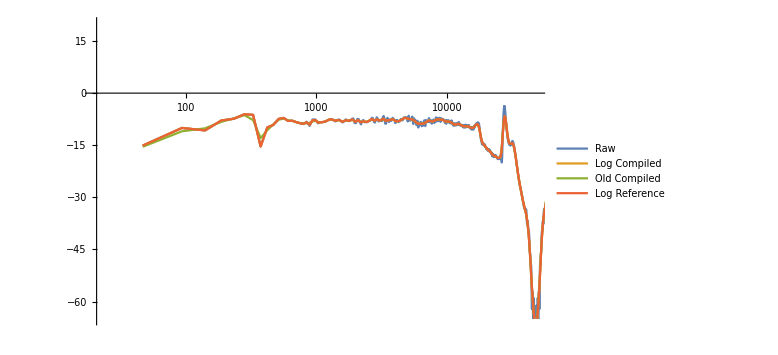

```mathematica
ListLogLinearPlot[{Transpose[{FreqVec,20Log10[Abs[RawTF]]}],Transpose[{FreqVec,LogSmoothTFdB}],Transpose[{FreqVec,OldSmoothTFdB}],Transpose[{FreqVec,RefSmoothTFdB}]},Joined->True,ImageSize->Large,PlotRange->{{20,48000},{-65,20}},PlotLegends->{"Raw","Log Compiled","Old Compiled","Log Reference"}]
```